# ADITYA KUMAR | 220211204 |BSC STATISTICS HONS SUB - LAB TEST PRACTICAL 1

{{y[x]→ⅇ^x C[3]+ⅇ^x C[2] Cos[x]+ⅇ^x C[1] Sin[x]}}

-ⅇ^x+ⅇ^x Cos[x]-ⅇ^x Sin[x]

-3 ⅇ^x+2 ⅇ^x Cos[x]-ⅇ^x Sin[x]

-ⅇ^x+3 ⅇ^x Cos[x]-ⅇ^x Sin[x]

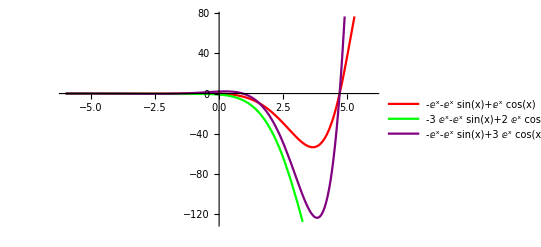

```mathematica
Sol = DSolve[y'''[x] - 3y''[x] + 4y'[x]-2y[x] == 0, y[x], x]
Sol1 = y[x] /. Sol[[1]] /. {C[1] -> -1, C[2] ->1, C[3] -> -1}
Sol2 = y[x] /. Sol[[1]] /. {C[1] -> -1, C[2] ->2, C[3] -> -3}
Sol3 = y[x] /. Sol[[1]] /. {C[1] -> -1, C[2] ->3, C[3] -> -1}
Plot[{Sol1, Sol2, Sol3}, {x, 6,-6},
PlotStyle -> {{Red}, {Green}, {Purple}},
PlotLegends -> {Sol1, Sol2, Sol3}]
```

## 3

```mathematica
u[x,y]*4(x+y)*D[u[x,y],x]+u[x,y]*4(x-y)*D[u[x,y],y] ==x*x+y*y
DSolve[{u[x,y]*4(x+y)*D[u[x,y],x]+u[x,y]*4(x-y)*D[u[x,y],y] == (x*x)+(y*y),u[x,2 x] ==0},u[x,y],{x,y}]
Plot3D[u[x,y]/.%,{x,0,6},{y,0,5}]
```

4 (x-y) u[x,y] u^(0,1)[x,y]+4 (x+y) u[x,y] u^(1,0)[x,y]==x^2+y^2

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u[x,y]→-(√(2 x^2+3 x y-2 y^2))/(√14)},{u[x,y]→(√(2 x^2+3 x y-2 y^2))/(√14)},{u[x,y]→-(√(2 x^2+3 x y-2 y^2))/(√14)},{u[x,y]→(√(2 x^2+3 x y-2 y^2))/(√14)}}

-Graphics3D-